# Inspect results

### Load data

```mathematica
toPs = 5.31915
```

5.31915

No closure

```mathematica
(**)
Clear[rawdataChi20,headersChi20,dataChi20,nnChi20];
rawdataChi20 = Import[NotebookDirectory[]<>"Sample_evol/measurements_Chi20.dat","Table"];
headersChi20 = Drop[rawdataChi20[[1]],1];
dataChi20 = Drop[rawdataChi20,1];
nnChi20=Length[dataChi20[[All,11]]]
```

500

```mathematica
Clear[rawdataChi8,headersChi8,dataChi8,nnChi8];
rawdataChi8 = Import[NotebookDirectory[]<>"Sample_evol/measurements_Chi8.dat","Table"];
headersChi8 = Drop[rawdataChi8[[1]],1];
dataChi8 = Drop[rawdataChi8,1];
nnChi8=Length[dataChi8[[All,11]]]
```

500

Data Alex

```mathematica
Clear[dataAlex];
dataAlex=Import[NotebookDirectory[]<>"Sample_evol/meas_alex_sys.csv","Table","FieldSeparators"->{";"}];
Clear[dataAlexN10];
dataAlexN10=Import[NotebookDirectory[]<>"Sample_evol/meas_alex_N10.csv","Table","FieldSeparators"->{";"}];
```

Data MC

```mathematica
(*MC Data M=20 N=6*)
rawdataMC = Import[NotebookDirectory[]<>"Sample_evol/measurements_MC_N6_Chi20_2.dat","Table"];
headersMC = Drop[rawdataMC[[1]],1];
dataMC = Drop[rawdataMC,1];
nnMC=Length[dataMC[[All]]]
```

37

```mathematica
headersMC
```

{time,N_11,N_21,N_31,N_32,N_33,N_34,N_35,N_36,N_37,Sx_1,Sz_1,re_over,im_over,Norm}

### System overlap

```mathematica
headersMC
```

{time,N_11,N_21,N_31,N_32,N_33,N_34,N_35,N_36,N_37,Sx_1,Sz_1,re_over,im_over,Norm}

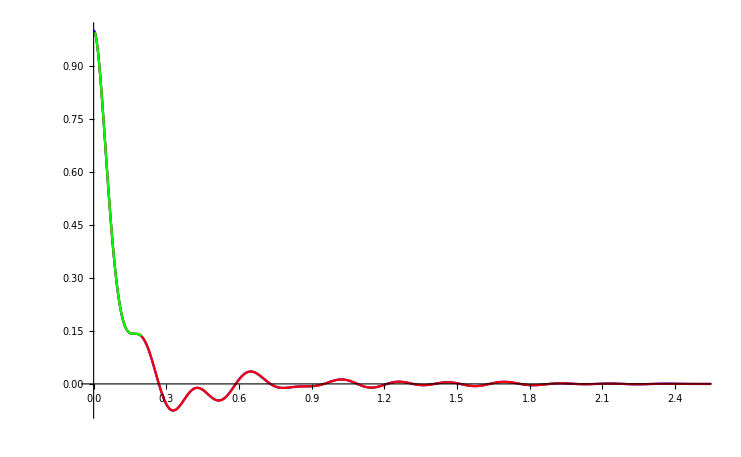

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlex[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True,PlotStyle->Blue],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,12]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,13]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
]
```

### Population chain site 10

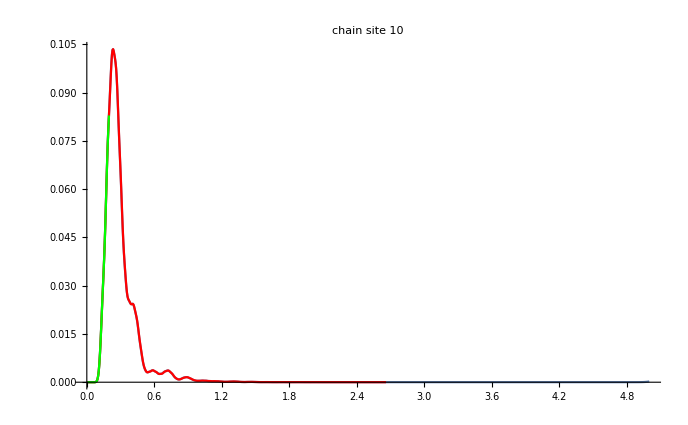

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,2]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,2]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green],
PlotRange->All,
PlotLabel->"chain site 10"
]
```

### Population chain site 20

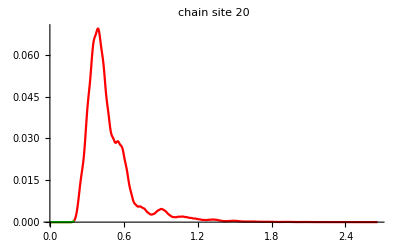

```mathematica
Show[
(*ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],*)
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,3]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,3]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green],
PlotRange->All,
PlotLabel->"chain site 20"
]
```

### Population chain site 40

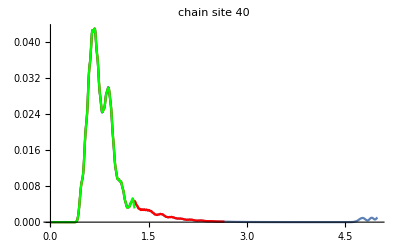

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,3]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,5]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,5]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green],
PlotRange->All,
PlotLabel->"chain site 40"
]
```

```mathematica
headersMC
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,Sx_1,Sz_1,re_over,im_over,Norm}

### Population chain site 80

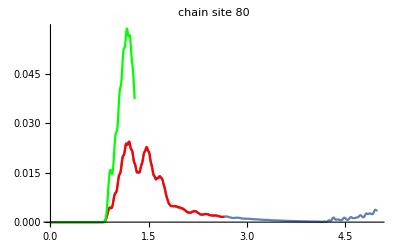

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlexN10[[All,5]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,9]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,9]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green],
PlotRange->All,
PlotLabel->"chain site 80"
]
```

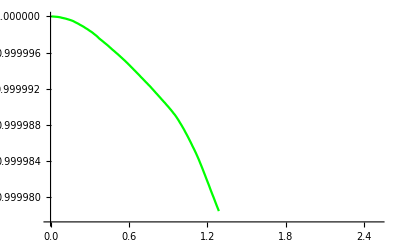

```mathematica
ListPlot[Transpose[{dataMC[[All,1]]*toPs,dataMC[[All,14]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
```

## Other things

```mathematica
Clear[rawdataChi20,headersChi20,dataChi20,nnChi20];
rawdataChi20 = Import[NotebookDirectory[]<>"Sample_evol/measurements_Chi20.dat","Table"];
headersChi20 = Drop[rawdataChi20[[1]],1];
dataChi20 = Drop[rawdataChi20,1];
nnChi20=Length[dataChi20[[All,11]]]
```

474

```mathematica
Clear[rawdataChi8,headersChi8,dataChi8,nnChi8];
rawdataChi8 = Import[NotebookDirectory[]<>"Sample_evol/measurements_Chi8.dat","Table"];
headersChi8 = Drop[rawdataChi8[[1]],1];
dataChi8 = Drop[rawdataChi8,1];
nnChi8=Length[dataChi8[[All,11]]]
```

486

```mathematica
dataChi8[[All,2]];
```

```mathematica
Clear[dataAlex];
dataAlex=Import[NotebookDirectory[]<>"Sample_evol/meas_alex_sys.csv","Table","FieldSeparators"->{";"}]
```

```mathematica
Clear[dataAlexN10];
dataAlexN10=Import[NotebookDirectory[]<>"Sample_evol/meas_alex_N10.csv","Table","FieldSeparators"->{";"}]
```

{{0.000188365,9.90494×10^-15,8.93295×10^-18,6.20078×10^-18,1.06856×10^-18,1.},4997,{0.941637,0.000233807,0.0010352,0.00159925,0.00364971,1.}}
 |  |  |  |

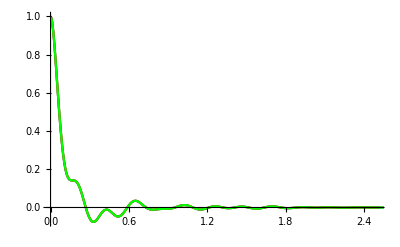

```mathematica
Show[
ListPlot[Transpose[{dataAlex[[All,1]]/0.188365,dataAlex[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,12]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataChi8[[All,1]]*toPs,dataChi8[[All,12]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
]
```

```mathematica
headersChi8
```

{time,N_10,N_20,N_30,N_40,N_50,N_60,N_70,N_80,Sx_1,Sz_1,re_over,im_over}

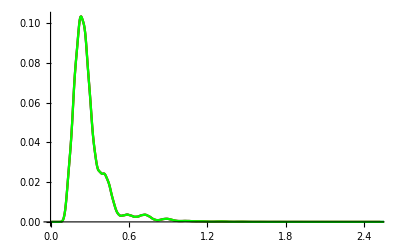

```mathematica
Show[
ListPlot[Transpose[{dataAlexN10[[All,1]]/0.188365,dataAlexN10[[All,2]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,2]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataChi8[[All,1]]*toPs,dataChi8[[All,2]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
]
```

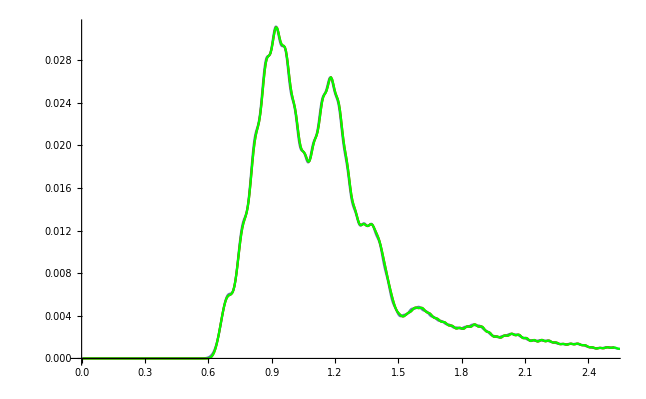

```mathematica
Show[
ListPlot[Transpose[{dataAlexN10[[All,1]]/0.188365,dataAlexN10[[All,4]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,7]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataChi8[[All,1]]*toPs,dataChi8[[All,7]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
]
```

```mathematica
headersChi20
```

{time,N_11,N_21,N_31,N_41,N_51,N_61,N_71,N_81,Sx_1,Sz_1,re_over,im_over}

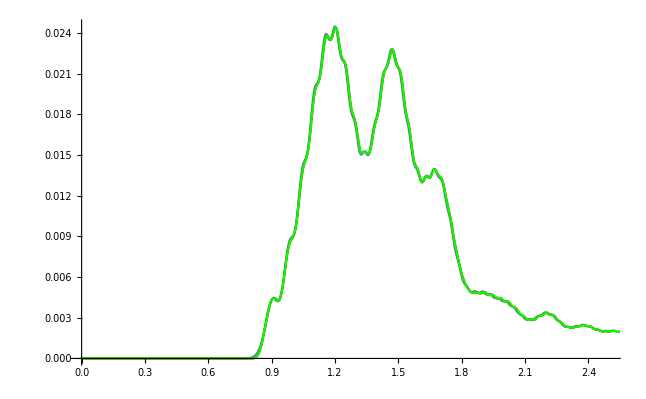

```mathematica
Show[
ListPlot[Transpose[{dataAlexN10[[All,1]]/0.188365,dataAlexN10[[All,5]]}],PlotRange->{{0,2.5},All},Joined->True],
ListPlot[Transpose[{dataChi20[[All,1]]*toPs,dataChi20[[All,9]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Red],
ListPlot[Transpose[{dataChi8[[All,1]]*toPs,dataChi8[[All,9]]}],Joined->True,PlotRange->{{0,2.5},All},PlotStyle->Green]
]
```